# Practicals 1 date: 01/19/23

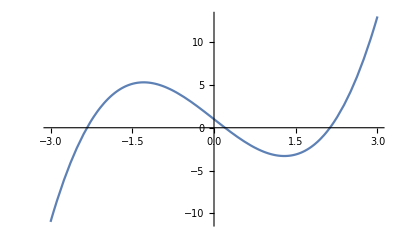

1  1.  0.25

2  0.25  0.186441

3  0.186441  0.201736

4  0.201736  0.20164

5  0.20164  0.20164

root = 0.20164

```mathematica
secantMethod[f_, xo_, xo1_, n_] := Module[{}, 
prev=N[xo];
next=N[xo1];
i=1;
While[i ≤n,
temp = next;
next = (prev*f[next]-next*f[prev])/(f[next]-f[prev]);
prev = temp;
Print[i, "  ", prev, "  ", next];
i++;];
Print["root = ", next]]
f[x_]=x^3-5x+1;
Plot[f[x], {x, -3, 3}]
secantMethod[f, 0, 1,5]
```

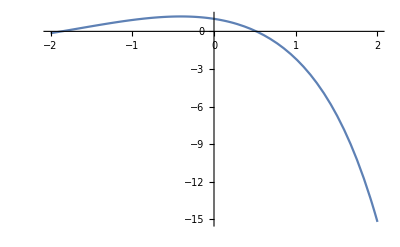

```mathematica
f[x_] = Cos[x] - x*Exp[x];
Plot[f[x], {x, -2, 2}]
```

```mathematica
regulaFalsi[f, 0, 1, 5]
```

1  1.  0.314665

2  0.314665  0.446728

3  0.446728  0.531706

4  0.531706  0.516904

5  0.516904  0.517747

root = 0.517747

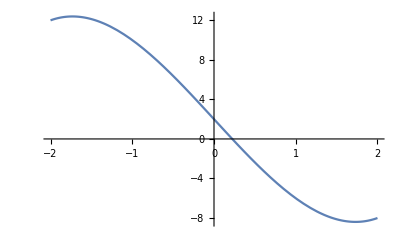

```mathematica
f[x_] = x^3-9*x +2;
Plot[f[x], {x, -2,2}]
```

```mathematica
regulaFalsi[f, 0, 1, 5]
```

1  1.  0.25

2  0.25  0.219512

3  0.219512  0.22347

4  0.22347  0.223462

5  0.223462  0.223462

root = 0.223462